```mathematica
Clear@Evaluate[Context[]<>"*"]
```

```mathematica
Δ[r_]=r^2-2 M r+a^2;
Σ[r_,θ_]=r^2+a^2 Cos[θ]^2;
ρ[r_,θ_]=r+ⅈ a Cos[θ];
𝒦[r_]=(r^2+a^2) ω-a m;
ruleK={κ->Collect[Expand[𝒦[rp+rp x]]/rp/.{c_ a^2+c_ rp^2->c 2 M rp}/.{a->2 M Ω̄,ω->(ω̄)/rp},M,Factor]/.{ω̄-m Ω̄->(χ rp)/(2 M)}};
```

```mathematica
eq0=(x(x+τ))^-s D[((x(x+τ))^(s+1)R'[x]), x]+((κ^2-I s(2x+τ)κ)/(x(x+τ))-λ+4I s ω̄ (1+x))R[x];
Eq=eq0/.ruleK;
```

```mathematica
h[l_]=((l^2-(kp+km)^2) (l^2-(kp-km)^2) (l^2-s^2))/(2 (l^2-1/4) l^3)/.{kp+km->Max[Abs[s],Abs[l]],kp-km->(s m)/Max[Abs[s],Abs[l]]};
EigenCoef={l+l^2-s (1+s),-(2 m s^2)/(l (1+l)),h[l+1]-h[l]-1,(2 h[l] m s^2)/((l-1) l^2 (l+1))-(2 h[l+1] m s^2)/((l+1)^2 l (l+2)),m^2 s^4 ((4 h[l+1])/(l^2 (l+1)^4 (l+2)^2)-(4 h[l])/((l-1)^2 l^4 (l+1)^2))-((l+2) h[l+1] h[l+2])/(2 (l+1) (2 l+3))+h[l+1]^2/(2 (l+1))+(h[l] h[l+1])/(2 l (l+1))-h[l]^2/(2 l)+((l-1) h[l-1] h[l])/(2 l (2 l-1)),m^3 s^6 ((8 h[l])/(l^6 (l+1)^3 (l-1)^3)-(8 h[l+1])/(l^3 (l+1)^6 (l+2)^3))+m s^2 h[l] (-(h[l+1] (7 l^2+7 l+4))/(l^3 (l+2) (l+1)^3 (l-1))-(h[l-1] (3 l-4))/(l^3 (l+1) (2 l-1) (l-2)))+m s^2 (((3 l+7) h[l+1] h[l+2])/(l (l+1)^3 (l+3) (2 l+3))-(3 h[l+1]^2)/(l (l+1)^3 (l+2))+(3 h[l]^2)/((l-1) l^3 (l+1)))};
```

```mathematica
nCoef=3;
RuleR={R->Function[x,x^(-s-(ⅈ χ)/τ) f[x]]};
RuleF={f->Function[x,∑_(n=0)^nCoef 𝒶[n] x^n]};
RuleParams={τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),rp->1+√(1-𝒥^2),
λ->EigenCoef.Table[((𝒥 ω̄)/rp)^n,{n,0,Length[EigenCoef]-1}]/.l->l+ϵ};
FreeParams={s->1,l->1,m->1,𝒥->0.9};
RuleBoundaryBHole={𝒶[0]->1};
ReplaceParams:=Limit[PowerExpand[#1//.RuleParams/.FreeParams],ϵ->0]&;
```

```mathematica
EquationF=Simplify[x^(s+(ⅈ χ)/τ) x (x+τ) (Eq/.RuleR)];
```

```mathematica
CoefList=CoefficientList[ReplaceParams[EquationF]/.RuleF,x]⟦;;nCoef+1⟧==0//Rationalize;
SolCoef=First@Solve[CoefList,Evaluate[Table[𝒶[n],{n,1,nCoef}]]]//Chop//Rationalize;
```

```mathematica
x0=10^-12.;
xM:=5000/ω̄;
omegaTable=Range[0.4,0.5,0.002]//DeleteCases[#,ReplaceParams[m Ω̄]]&;
SolF=ParallelTable[
Print[ω̄];
First@First@NDSolve[{ReplaceParams[EquationF]==0,{f[x0],f'[x0]}==({f[x0],f'[x0]}/.RuleF/.SolCoef/.RuleBoundaryBHole)},f,{x,x0,xM},PrecisionGoal->12,AccuracyGoal->20,MaxSteps->∞],
{ω̄,omegaTable}];
SolωF={Thread[ω̄->omegaTable],SolF}ᵀ;
```

0.4

0.41

0.42

0.428

0.43

0.412

0.402

0.422

0.432

0.414

0.404

0.424

0.434

0.406

0.416

0.426

0.408

0.418

0.436

0.444

0.438

0.454

0.446

0.44

0.456

0.448

0.452

0.462

0.47

0.458

0.442

0.464

0.472

0.46

0.466

0.474

0.478

0.486

0.468

0.488

0.48

0.476

0.49

0.482

0.492

0.494

0.484

0.496

0.498

0.5

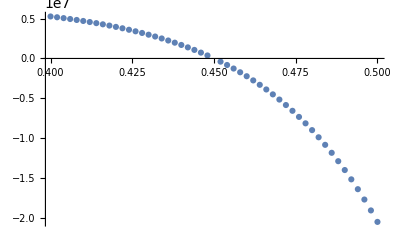

```mathematica
{ω̄,ReplaceParams[-(ω̄/χ)/(Abs[f[xM](xM/τ)^(-s-I χ/τ)]^2)]}/.SolωF//ListPlot
```

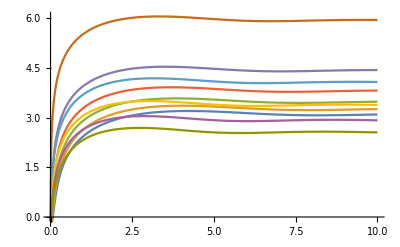

```mathematica
Plot[Log@Abs@f[x]/.SolωF[[Range[1,Length@SolωF,5]]]//Evaluate,{x,x0,10},PlotRange->All]
```

```mathematica
Normal@Series[(x/τ)^(-s-(ⅈ χ)/τ) 𝒜 (x/τ+1)^((ⅈ χ)/τ) Hypergeometric2F1[-l,1+l,1-s-(2ⅈ χ)/τ,-x/τ],{x,0,3}]//PowerExpand//Simplify
```

x^(-s-(ⅈ χ)/τ) 𝒜 τ^(s+(ⅈ χ)/τ) (1+x ((l (1+l))/(τ-s τ-2 ⅈ χ)+(ⅈ χ)/τ^2)+1/2 x^2 (((-1+l) l (1+l) (2+l))/(((-2+s) τ+2 ⅈ χ) ((-1+s) τ+2 ⅈ χ))-(2 ⅈ l (1+l) χ)/(τ^2 ((-1+s) τ+2 ⅈ χ))-(χ (ⅈ τ+χ))/τ^4)+1/6 x^3 (-((-2+l) (-1+l) l (1+l) (2+l) (3+l))/(((-3+s) τ+2 ⅈ χ) ((-2+s) τ+2 ⅈ χ) ((-1+s) τ+2 ⅈ χ))+(3 ⅈ (-1+l) l (1+l) (2+l) χ)/(τ^2 ((-2+s) τ+2 ⅈ χ) ((-1+s) τ+2 ⅈ χ))+(3 l (1+l) χ (ⅈ τ+χ))/(τ^4 ((-1+s) τ+2 ⅈ χ))+(χ (2 ⅈ τ^2+3 τ χ-ⅈ χ^2))/τ^6))